# Assets implicated in a lasso

### Graphs

Consider a list of assets, which implicate other assets, and the directed graph resulting:

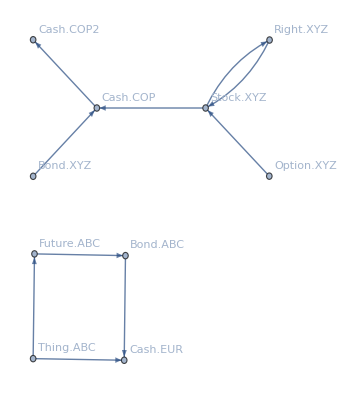

```mathematica
g=Graph[{"Right.XYZ"-> "Stock.XYZ",
"Stock.XYZ"-> "Cash.COP",
"Stock.XYZ"-> "Right.XYZ",
"Cash.COP"->"Cash.COP2",
"Bond.XYZ"-> "Cash.COP",
"Option.XYZ"-> "Stock.XYZ",
"Bond.ABC"-> "Cash.EUR",
"Future.ABC"-> "Bond.ABC",
"Thing.ABC"-> "Future.ABC",
"Thing.ABC"-> "Cash.EUR"}, VertexLabels->"Name"]
```

```mathematica
VertexList[g]
```

{Right.XYZ,Stock.XYZ,Cash.COP,Cash.COP2,Bond.XYZ,Option.XYZ,Bond.ABC,Cash.EUR,Future.ABC,Thing.ABC}

#### Adjacency matrix

The list of directly directed connections is the adjacency matrix:

```mathematica
AdjacencyMatrix[g]//Normal//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)

Determine connections of a vertex to other vertices

```mathematica
IncidenceList[g,"Cash.COP",1]
```

{Stock.XYZ->Cash.COP,Cash.COP->Cash.COP2,Bond.XYZ->Cash.COP}

```mathematica
IncidenceList[g,"Cash.COP",3]
```

{Right.XYZ->Stock.XYZ,Stock.XYZ->Cash.COP,Stock.XYZ->Right.XYZ,Cash.COP->Cash.COP2,Bond.XYZ->Cash.COP,Option.XYZ->Stock.XYZ}

Get a list of vertices that are at a distance of at most d

```mathematica
AdjacencyList[g,"Cash.COP",1]
```

{Stock.XYZ,Cash.COP2,Bond.XYZ}

```mathematica
AdjacencyList[g,"Cash.COP",Infinity]
```

{Right.XYZ,Stock.XYZ,Cash.COP2,Bond.XYZ,Option.XYZ}

In both AdjacencyList and IncidenceList the downstream directed vertices and upstream indicated vertices are included equally

#### Graph distance matrix

Directed distance of each vertex to every other. The rows yield what each vertex influences (0 -> itself, 1 -> direct connection, > 1 = indirect connection, ∞ => no connection). The columns yield which vertices import that vertex. A number of algorithms can calculate this (Dijkstra, Floyd-Warshall, some others - see below sections).

```mathematica
gdm=GraphDistanceMatrix[g];
```

```mathematica
gdm//MatrixForm[#,TableHeadings->{VertexList[g],VertexList[g]}]&
```

( | Right.XYZ | Stock.XYZ | Cash.COP | Cash.COP2 | Bond.XYZ | Option.XYZ | Bond.ABC | Cash.EUR | Future.ABC | Thing.ABC
Right.XYZ | 0 | 1 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
Stock.XYZ | 1 | 0 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
Cash.COP | ∞ | ∞ | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
Cash.COP2 | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
Bond.XYZ | ∞ | ∞ | 1 | 2 | 0 | ∞ | ∞ | ∞ | ∞ | ∞
Option.XYZ | 2 | 1 | 2 | 3 | ∞ | 0 | ∞ | ∞ | ∞ | ∞
Bond.ABC | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | ∞ | ∞
Cash.EUR | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞
Future.ABC | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 0 | ∞
Thing.ABC | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 0)

The distances of the reverse graph is the transpose of the distance matrix

```mathematica
GraphDistanceMatrix[g//ReverseGraph]//MatrixForm[#,TableHeadings->{VertexList[g],VertexList[g]}]&
```

( | Right.XYZ | Stock.XYZ | Cash.COP | Cash.COP2 | Bond.XYZ | Option.XYZ | Bond.ABC | Cash.EUR | Future.ABC | Thing.ABC
Right.XYZ | 0 | 1 | ∞ | ∞ | ∞ | 2 | ∞ | ∞ | ∞ | ∞
Stock.XYZ | 1 | 0 | ∞ | ∞ | ∞ | 1 | ∞ | ∞ | ∞ | ∞
Cash.COP | 2 | 1 | 0 | ∞ | 1 | 2 | ∞ | ∞ | ∞ | ∞
Cash.COP2 | 3 | 2 | 1 | 0 | 2 | 3 | ∞ | ∞ | ∞ | ∞
Bond.XYZ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞
Option.XYZ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞
Bond.ABC | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | 1 | 2
Cash.EUR | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 2 | 1
Future.ABC | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1
Thing.ABC | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0)

Cash.COP depends on:

```mathematica
gdm[[VertexIndex[g,"Cash.COP"]]]
```

{∞,∞,0,1,∞,∞,∞,∞,∞,∞}

Assets which depend on Cash.COP:

```mathematica
gdm[[;;,VertexIndex[g,"Cash.COP"]]]
```

{2,1,0,∞,1,2,∞,∞,∞,∞}

Items influencing Cash.COP

```mathematica
Extract[VertexList[g],Position[gdm[[;;,VertexIndex[g,"Cash.COP"]]],Except[Infinity],{1},Heads->False]]
```

{Right.XYZ,Stock.XYZ,Cash.COP,Bond.XYZ,Option.XYZ}

Items influenced by Cash.COP

```mathematica
Extract[VertexList[g],Position[gdm[[VertexIndex[g,"Cash.COP"]]],Except[Infinity],{1},Heads->False]]
```

{Cash.COP,Cash.COP2}

```mathematica
Extract[VertexList[g],Position[gdm[[VertexIndex[g,"Bond.ABC"]]],Except[Infinity],{1},Heads->False]]
```

{Bond.ABC,Cash.EUR}

Specific calculation of graph distances:

```mathematica
GraphDistance[g,"Cash.COP"]
```

{∞,∞,0,1,∞,∞,∞,∞,∞,∞}

```mathematica
GraphDistance[ReverseGraph@g,"Cash.COP"]
```

{2,1,0,∞,1,2,∞,∞,∞,∞}

## Examples

General documentation and pseudocode for algorithm

https://en.wikipedia.org/wiki/Floyd%E2%80%93Warshall_algorithm

Super interesting use case...

https://www.boost.org/doc/libs/1_70_0/libs/graph/doc/file_dependency_example.html

## Reachability matrix

Infer direct connections between each and every vertex via intermediate vertices. Need to compute the transitive closure of the binary relation (being the adjacency matrix).

### Using Mathematica

TransitiveClosureGraph calculates the graph of every vertex connected to every other using known intermediate vertices:

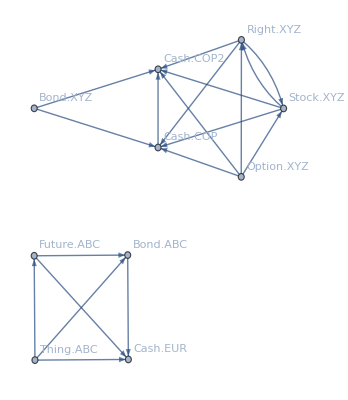

```mathematica
TransitiveClosureGraph[g,VertexLabels->Automatic]
```

The adjacency matrix of this graph is the ReachablityMatrix

```mathematica
AdjacencyMatrix@TransitiveClosureGraph[g]//MatrixForm
```

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)

### Manually

Note a little fiddling is required for the diagonal elements

```mathematica
x=IdentityMatrix[10]+Total@Table[MatrixPower[AdjacencyMatrix[g],i]//Normal,{i,1,10}];
MatrixForm@x
```

(6 | 5 | 5 | 4 | 0 | 0 | 0 | 0 | 0 | 0
5 | 6 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
5 | 5 | 5 | 4 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 1)

```mathematica
(x/.n_/;n>0->1)-IdentityMatrix[10]//MatrixForm
```

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)

### Warshall’s algorithm

Warshall’s algorithm is a modified version of the Floyd-Warshall algorithm. The path length function is modified with Boolean operations, such that min(...)→ ...||... and ...+...→ ...&&.... By storing booleans, the storage is smaller and the performance is slightly faster by a constant factor; the complexity remains O(N^3).

Require the adjacency matrix in Boolean form:

```mathematica
adjBool=Map[(#≠ 0)&,Normal[AdjacencyMatrix[g]],{2}];
MatrixForm@adjBool
```

(False | True | False | False | False | False | False | False | False | False
True | False | True | False | False | False | False | False | False | False
False | False | False | True | False | False | False | False | False | False
False | False | False | False | False | False | False | False | False | False
False | False | True | False | False | False | False | False | False | False
False | True | False | False | False | False | False | False | False | False
False | False | False | False | False | False | False | True | False | False
False | False | False | False | False | False | False | False | False | False
False | False | False | False | False | False | True | False | False | False
False | False | False | False | False | False | False | True | True | False)

```mathematica
MatrixQ[adjBool,BooleanQ]
```

True

Use a recursive definition of the Warshall algorithm. In Mathematica the use of “memoization” gives an important improvement to performance but this requires k not be “too big” otherwise we’ll blow out the memory.

```mathematica
Clear@pathD;
pathD[adjB_/;MatrixQ[adjBool,BooleanQ]][i_,j_,0]:=
pathD[adjB][i,j,0]=adjB[[i,j]];
pathD[adjB_][i_,j_,k_]:=pathD[adjB][i,j,k]=
pathD[adjB][i,j,k-1]||(pathD[adjB][i,k,k-1]&&pathD[adjB][k,j,k-1]);
```

```mathematica
warshallSoln=Boole/@MapIndexed[pathD[adjBool][First@#2,Last@#2,10]&,adjBool,{2}];
```

```mathematica
warshallSoln//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)

```mathematica
warshallSoln
```

{{1,1,1,1,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1,1,0}}

Suspect that the variation in the diagonal elements indicates self-cycles?

```mathematica
(warshallSoln-AdjacencyMatrix@TransitiveClosureGraph[g])//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Using a potentially more efficient Fold construct - this is closer to a procedural programming approach

```mathematica
fSoln=Boole/@Fold[Table[#1⟦i,j⟧||(#1⟦i,#2⟧&&#1⟦#2,j⟧),{j,1,10},{i,1,10}]&,adjBool,Range[10]];
```

```mathematica
MatrixForm@fSoln
```

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)

Interestingly the recursive technique is faster than folding. For very large graphs this is unlikely to hold.

```mathematica
RepeatedTiming[Boole/@Fold[Table[#1[[i,j]]||(#1[[i,#2]]&&#1[[#2,j]]),{j,1,10},{i,1,10}]&,adjBool,Range[10]];]
```

{0.0011,Null}

```mathematica
RepeatedTiming[Boole/@MapIndexed[pathD[adjBool][First@#2,Last@#2,10]&,adjBool,{2}];]
```

{0.00017,Null}